```mathematica
ClearAll["Global`*"]
```

```mathematica
<<HypothesisTesting`
```

1.31579

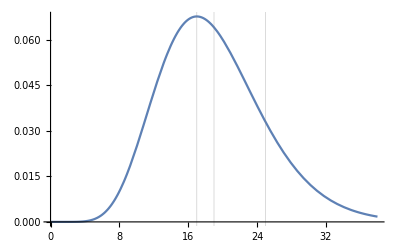

0.839458

0.160542

OneSidedPValue→0.160542

```mathematica
DoF=19;
χ2=25;
χ2/DoF//N
Plot[PDF[ChiSquareDistribution[DoF],x],{x,0,2DoF},GridLines->{{χ2,DoF,DoF-2},{}}]
pVall=Integrate[PDF[ChiSquareDistribution[DoF],x],{x,0,χ2}]//N
pValr=Integrate[PDF[ChiSquareDistribution[DoF],x],{x,χ2,∞}]//N
ChiSquarePValue[χ2,DoF]
```

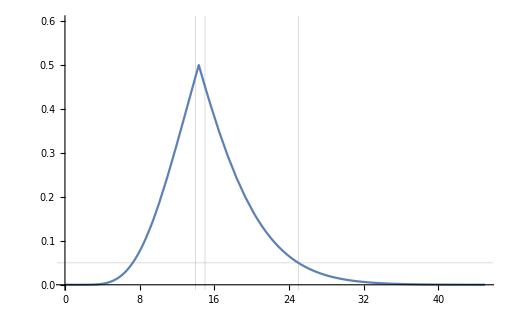

```mathematica
Plot[OneSidedPValue/.ChiSquarePValue[x,DoF],{x,0,3DoF},PlotRange->{0,0.6},GridLines->{{DoF-1,DoF,χ2},{pVall,pValr}}]
```

### Konfidenzintervalle für 5 % und 1 % Signifikanzlevel

```mathematica
NSolve[Assuming[χ2t>0,Integrate[PDF[ChiSquareDistribution[DoF+0.001],x],{x,χ2t,∞}]]==0.05,χ2t]
NSolve[Assuming[χ2t>0,Integrate[PDF[ChiSquareDistribution[DoF+0.0001],x],{x,χ2t,∞}]]==0.01,χ2t]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{χ2t→30.1448}}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{χ2t→36.191}}